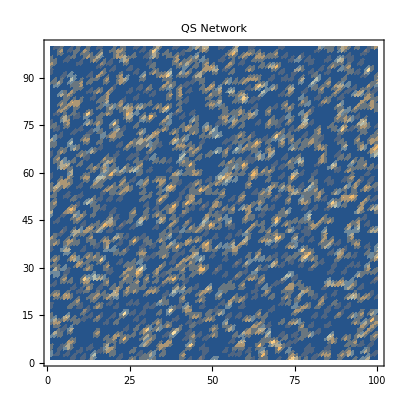

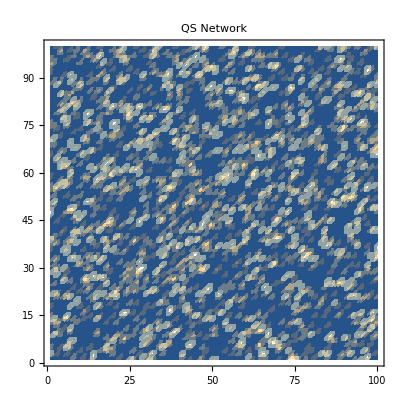

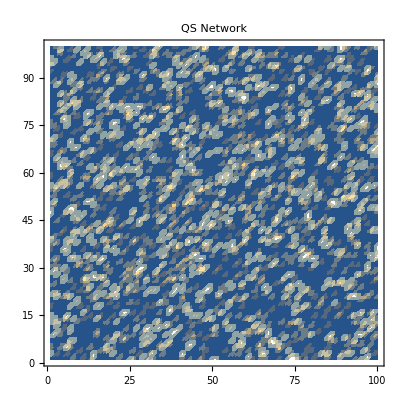

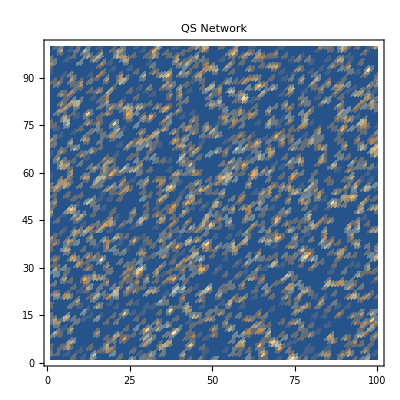

Append::normal: Nonatomic expression expected at position 1 in Append[1,1].

Append::normal: Nonatomic expression expected at position 1 in Append[51,51].

Append::argt: Append called with 3 arguments; 1 or 2 arguments are expected.

Append::argt: Append called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Append::argt will be suppressed during this calculation.

Part::partw: Part 401 of {{1,46},{1,51},{1,66},{1,70},{1,76},{1,78},{2,11},{2,22},{2,81},{2,89},{3,1},{3,31},{3,32},{3,56},{3,83},{3,84},{4,48},{4,65},{4,96},{5,1},{5,4},{5,6},{5,18},{5,20},{5,47},{5,70},{5,71},{5,79},{6,93},{7,7},{7,8},{7,20},{7,59},{8,18},{8,32},{8,42},{8,48},{8,66},{8,72},{8,85},{9,31},{9,99},{10,60},{11,34},{11,40},{11,65},{12,36},{12,54},{12,77},{12,99},«350»} does not exist.

Set::shape: Lists {c,d} and {{1,46},{1,51},{1,66},{1,70},{1,76},{1,78},{2,11},{2,22},{2,81},{2,89},{3,1},{3,31},{3,32},{3,56},{3,83},{3,84},{4,48},{4,65},{4,96},{5,1},{5,4},{5,6},{5,18},{5,20},{5,47},{5,70},{5,71},{5,79},{6,93},{7,7},{7,8},{7,20},{7,59},{8,18},{8,32},{8,42},{8,48},{8,66},{8,72},{8,85},{9,31},{9,99},{10,60},{11,34},{11,40},{11,65},{12,36},{12,54},{12,77},{12,99},«350»}⟦401⟧ are not the same shape.

Part::partw: Part 402 of {{1,46},{1,51},{1,66},{1,70},{1,76},{1,78},{2,11},{2,22},{2,81},{2,89},{3,1},{3,31},{3,32},{3,56},{3,83},{3,84},{4,48},{4,65},{4,96},{5,1},{5,4},{5,6},{5,18},{5,20},{5,47},{5,70},{5,71},{5,79},{6,93},{7,7},{7,8},{7,20},{7,59},{8,18},{8,32},{8,42},{8,48},{8,66},{8,72},{8,85},{9,31},{9,99},{10,60},{11,34},{11,40},{11,65},{12,36},{12,54},{12,77},{12,99},«350»} does not exist.

Set::shape: Lists {c,d} and {{1,46},{1,51},{1,66},{1,70},{1,76},{1,78},{2,11},{2,22},{2,81},{2,89},{3,1},{3,31},{3,32},{3,56},{3,83},{3,84},{4,48},{4,65},{4,96},{5,1},{5,4},{5,6},{5,18},{5,20},{5,47},{5,70},{5,71},{5,79},{6,93},{7,7},{7,8},{7,20},{7,59},{8,18},{8,32},{8,42},{8,48},{8,66},{8,72},{8,85},{9,31},{9,99},{10,60},{11,34},{11,40},{11,65},{12,36},{12,54},{12,77},{12,99},«350»}⟦402⟧ are not the same shape.

Part::partw: Part 403 of {{1,46},{1,51},{1,66},{1,70},{1,76},{1,78},{2,11},{2,22},{2,81},{2,89},{3,1},{3,31},{3,32},{3,56},{3,83},{3,84},{4,48},{4,65},{4,96},{5,1},{5,4},{5,6},{5,18},{5,20},{5,47},{5,70},{5,71},{5,79},{6,93},{7,7},{7,8},{7,20},{7,59},{8,18},{8,32},{8,42},{8,48},{8,66},{8,72},{8,85},{9,31},{9,99},{10,60},{11,34},{11,40},{11,65},{12,36},{12,54},{12,77},{12,99},«350»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::shape: Lists {c,d} and {{1,46},{1,51},{1,66},{1,70},{1,76},{1,78},{2,11},{2,22},{2,81},{2,89},{3,1},{3,31},{3,32},{3,56},{3,83},{3,84},{4,48},{4,65},{4,96},{5,1},{5,4},{5,6},{5,18},{5,20},{5,47},{5,70},{5,71},{5,79},{6,93},{7,7},{7,8},{7,20},{7,59},{8,18},{8,32},{8,42},{8,48},{8,66},{8,72},{8,85},{9,31},{9,99},{10,60},{11,34},{11,40},{11,65},{12,36},{12,54},{12,77},{12,99},«350»}⟦403⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

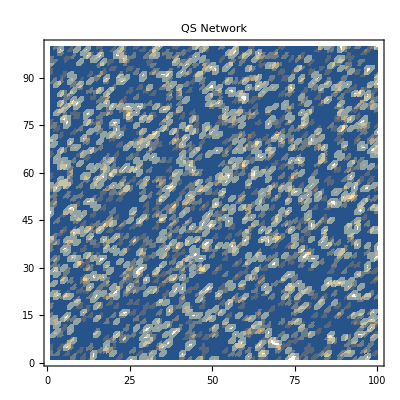

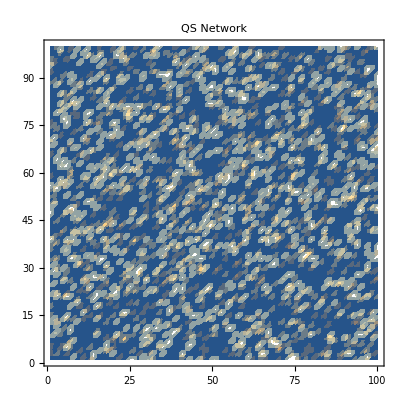

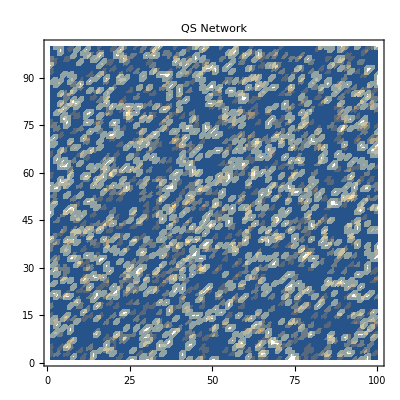

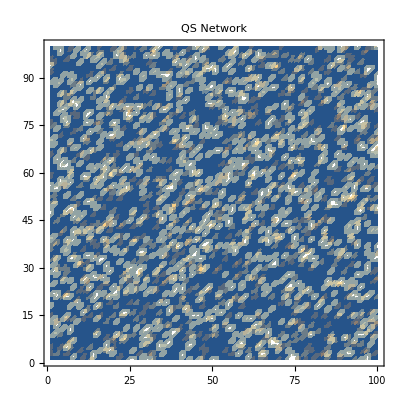

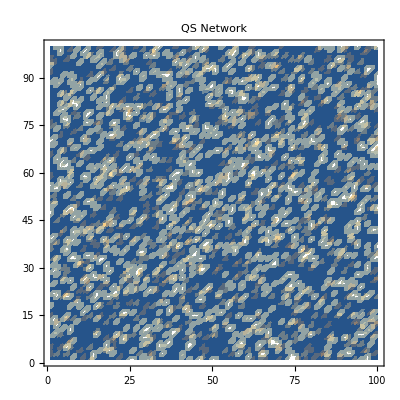

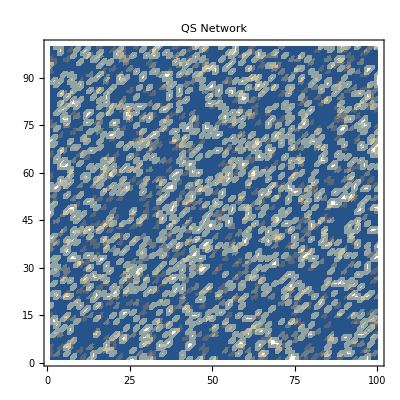

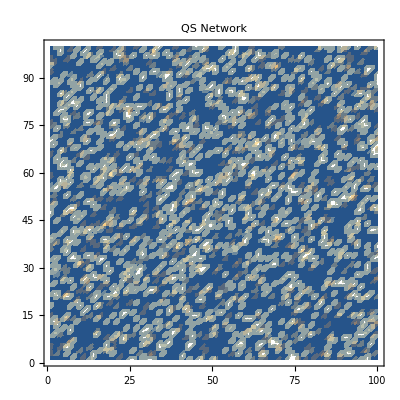

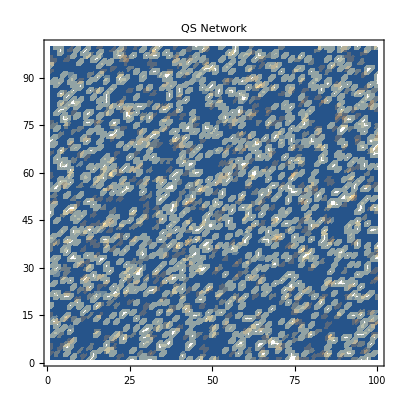

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

$Aborted

```mathematica
areaSize=100;
cellDensity=0.2;
observationTime=20;
timeforSignaling=1;

cellDistribution[]:=HalfNormalDistribution[0.5];

(*Auxiliary signalling functions*)
neigh={};
For[k=1,k≤15,k++,
neighborhood=Table[Max[0,k-Abs[x]-Abs[y]],{x,-5,5},{y,-5,5}];
neigh=Append[neigh,neighborhood]]; 

aiDomain={1,2,3,4,5,6,7,8,9,10};

aiConcentration[level_]:=Switch[level,1,neigh[[3]],2,neigh[[5]],3,neigh[[7]],4,neigh[[9]],5,neigh[[8]],6,neigh[[7]],7,neigh[[6]],8,neigh[[5]],9,neigh[[4]],10,neigh[[3]]];

aiCell[level_]:=Switch[level,1,1,2,3,3,5,4,7,5,6,6,5,7,4,8,3,9,2,10,1];

aiDistance[level_]:=1+aiCell[level];

aiUpdate[levels_,lccore_]:=(levelsNew=levels;
cellPos1=Position[levels[[First[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]>First[aiDomain]+3,levelsNew[[First[aiDomain]+1]]=ReplacePart[levelsNew[[First[aiDomain]+1]],1,cellPos1[[s]]];levelsNew[[First[aiDomain]]]=ReplacePart[levelsNew[[First[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
cellPos1=Position[levels[[Last[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]<Last[aiDomain]+3,levelsNew[[Last[aiDomain]-1]]=ReplacePart[levelsNew[[Last[aiDomain]-1]],1,cellPos1[[s]]];
levelsNew[[Last[aiDomain]]]=ReplacePart[levelsNew[[Last[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
For[r=First[aiDomain]+1,r<Last[aiDomain],r++,
cellPos1=Position[levels[[r]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,
If[conc1[[s]]<r+3,levelsNew[[r-1]]=ReplacePart[levelsNew[[r-1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]],If[conc1[[s]]>r+3,levelsNew[[r+1]]=ReplacePart[levelsNew[[r+1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]]];];];
];

levelsNew
);

(*Initializing all necessary data structures*)
levels=Table[0,{Last[aiDomain]-First[aiDomain]+1},{areaSize},{areaSize}];
levelsDynamic=levels;
levelsDynamicNew=levels;
levelsStatic=levels;
graph=Range[observationTime];
productionList=Range[observationTime];
cells=Table[If[Random[]<cellDensity,1,0],{i,areaSize},{j,areaSize}];

levels=ReplacePart[levels,cells,1];
lc=ListCorrelate[aiConcentration[1],cells,{-1,1},0];
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
levels=aiUpdate[levels,lccore];

nCells=Count[cells,1,2];
cellPos=Position[cells,1];
EdgeMatrix=Table[0,{nCells},{nCells}];

(*Main QS cycle*)
For[clock=1,clock≤observationTime,clock++,
(*update level and concentration table*)
If[Mod[clock,timeforSignaling]==0,
lc=Plus@@Function[{i},ListCorrelate[aiConcentration[i],levels[[i]],{-1,1},0]]/@aiDomain;
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
signalingCells=cells; 
For[k=1,k≤nCells,k++,
(*To avoid artificial cyclic activation-inhibition dependencies, only a small fraction of cells is signalling at once*)
If[Random[]<.8,signalingCells=ReplacePart[signalingCells,0,cellPos[[k]]]];
];
For[k=First[aiDomain],k≤Last[aiDomain],k++,
levelsStatic[[k]]=levels[[k]]-signalingCells;
mins=Position[levelsStatic[[k]],-1];
For[v=1,v≤Length[mins],v++,levelsStatic[[k]]=ReplacePart[levelsStatic[[k]],0,mins[[v]]]];
];
levelsDynamic=levels-levelsStatic;
(*To update make the signal disappear at 4s*)
(**)
If[ clock>4 && clock < 15, x=1;
If[clock==5,
cp1=Position[Total[levelsDynamic],1];
{a,b}=cp1[[2]];
For[n=2,n≤1000,2*n++,{c,d}=cp1[[n]];(*Since no. of cells is 5000 n≤1000*)
a=Append[a,c];
b=Append[b,d];
];
];
For[x=1,x≤500,x++, (*n/2*)
lccore[[a[[x]],b[[x]]]]=0;
];
];

levelsDynamicNew=aiUpdate[levelsDynamic,lccore];
levels=levelsDynamicNew+levelsStatic;
];

x=0;
graph[[clock]]=Plus@@Function[{i},aiDistance[i]*levels[[i]]]/@aiDomain;
Print[ListDensityPlot[graph[[clock]],PlotLabel->"QS Network"]];
productionList[[clock]]=N[Total[graph[[clock]],2]/nCells](*average ai production per cell*)
]; 

(*Pathway Analysis*)
EdgeMatrix=Table[0,{nCells},{nCells}];
highlyConnectedCells=Table[0,{nCells}];
nHighlyConnected=0;
For[k=1,k≤nCells,k++,
maxDist=graph[[1]][[cellPos[[k,1]],cellPos[[k,2]]]];
For[v=1,v≤nCells,v++,
If[k==v,Continue[]];
dist=Abs[cellPos[[k,1]]-cellPos[[v,1]]]+Abs[cellPos[[k,2]]-cellPos[[v,2]]];
If[dist≤maxDist,EdgeMatrix[[k,v]]++];];
];
totalEdgeMatrix=Total[EdgeMatrix,{2}];
For[k=1,k≤nCells,k++,
If[totalEdgeMatrix[[k]]>5,nHighlyConnected++;highlyConnectedCells[[k]]=1];
];


(* To plot all unconncected nodes across time*)
(* Include before and after the node signal = 0*)
For[n=1,n ≤ 20,n++,
EdgeMatrix=Table[0,{nCells},{nCells}];
highlyConnectedCells=Table[0,{nCells}];
nHighlyConnected=0;
For[k=1,k≤nCells,k++,
maxDist=graph[[n]][[cellPos[[k,1]],cellPos[[k,2]]]];
For[v=1,v≤nCells,v++,
If[k==v,Continue[]];
dist=Abs[cellPos[[k,1]]-cellPos[[v,1]]]+Abs[cellPos[[k,2]]-cellPos[[v,2]]];
If[dist≤maxDist,EdgeMatrix[[k,v]]++];];
];
totalEdgeMatrix=Total[EdgeMatrix,{2}];
(**)For[k=1,k≤nCells,k++,
If[totalEdgeMatrix[[k]]>5,nHighlyConnected++;highlyConnectedCells[[k]]=1];
];


nLowConnected=0;

For[k=1,k≤nCells,k++,
If[totalEdgeMatrix[[k]]<5,nLowConnected++;

]];

nUnConnected=0;
For[k=1,k≤nCells,k++,
If[totalEdgeMatrix[[k]]==0,nUnConnected++;

]];
Print[nLowConnected]
Print[nUnConnected]
Print[Total[Total[EdgeMatrix]]]
Print[nCells]
]
```

```mathematica
ListLinePlot[productionList]
```

-Graphics-

```mathematica
productionList
```

{3.97923,4.38279,4.8091,5.20969,5.2453,5.56874,5.91296,6.27695,6.64787,7.02671,7.39169,7.69436,8.02176,8.39862,8.82394,9.23937,9.6459,10.0425,10.4392,10.817}

```mathematica
ListLinePlot[productionList]
```

-Graphics-

```mathematica
productionList
```

{3.95652,4.35079,4.73024,5.09684,5.07856,5.32757,5.53113,5.69565,5.85326,5.95257,6.01828,6.02767,6.0163,6.0168,6.00445,6.00049,5.9832,5.95899,5.90069,5.80287}

```mathematica
ListLinePlot[productionList]
```

```mathematica
ListLinePlot[productionList]
```

-Graphics-

```mathematica
productionList
```

{3.98638,4.3823,4.76119,5.11089,5.4178,5.67267,5.87646,6.08852,6.24611,6.36916,6.4392,6.46498,6.45817,6.44309,6.43434,6.37646,6.26994,6.16342,6.03745,5.91683}

```mathematica
productionList
```

{3.90542,4.29951,4.6601,5.04631,5.06552,5.29064,5.49113,5.67143,5.8197,5.91182,5.95862,5.99655,5.98473,5.98177,6.00246,6.00591,5.96502,5.91724,5.85567,5.7867}

```mathematica
productionList
```

{3.96308,4.33641,4.73026,5.08564,4.72359,4.91026,5.08615,5.18308,5.30821,5.41846,5.51333,5.5559,5.56769,5.58205,5.61333,5.65795,5.68,5.72103,5.73077,5.71795}